```mathematica
Using this notebook replace the data with your data.  Plot and fit the data with the function "Fit[data, {1,Sqrt[x]},x]".  Then using the "Show" command show the fit and data on one plot.  Make this plot publication ready by adding axes labels and units, etc.

each cells is executed by pressing SHIFT+ENTER
```

```mathematica
data={{2.,5.9},{2.4,5.52},{2.7,5.96},{3.1,6.4},{3.3,7.01},{3.7,7.23},{4.12,7.77},{4.9,8.2},{5.65,9.0},{5.72,9.2},{6.86,9.96}}
```

{{2.,5.9},{2.4,5.52},{2.7,5.96},{3.1,6.4},{3.3,7.01},{3.7,7.23},{4.12,7.77},{4.9,8.2},{5.65,9.},{5.72,9.2},{6.86,9.96}}

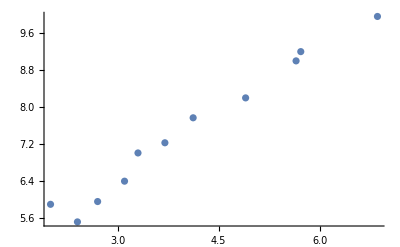

```mathematica
plot1=ListPlot@data
```

```mathematica
fit1=Fit[data, {1,Sqrt[x]},x]
```

-0.0365173+3.79748 √x

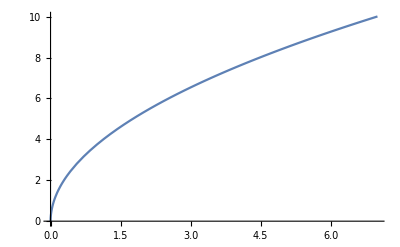

```mathematica
plot2=Plot[fit1,{x,0,7}]
```

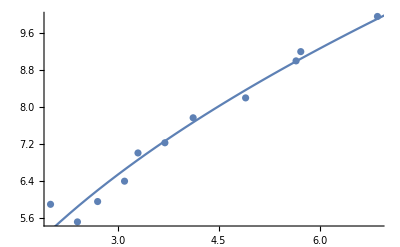

```mathematica
Show[plot1, plot2]
```

```mathematica
Now Linearize the data name it "datalinear" and plot T^2 vs m.  Then fit the data using "Fit[datalinear,{1,x},x]"  Display the fit and the data together with in a publication ready graph.
```